# Lecture 3 - Vicini

Accesso a LCM: i vari server hanno o mathematica 4 o mathematica 5.2.

```mathematica
Integrate[ConditionalExpression[E^(-x^2/(2 s^2)),s_Real],{x,-Infinity,Infinity}]
```

∫_(-∞)^∞ ConditionalExpression[ⅇ^(-x^2/(2 s^2)),s_Real]ⅆx

```mathematica
Clear[s]
```

```mathematica
FullForm[(1+x)^2]
```

Plus[1,Times[2,x],Power[x,2]]

```mathematica
FullForm[1+2x+x^2]
```

Plus[1,Times[2,x],Power[x,2]]

```mathematica
??Orderless
```

```mathematica
IdentityMatrix[3]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
IdentityMatrix[5]
```

{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}

```mathematica
MatrixForm[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}]
```

(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)

```mathematica
TableForm[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}]
```

1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1

```mathematica
Grid[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}]
```

1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1

#### Table

Table restituisce una lista di elementi, basandosi su un iteratorre. Gli si può dare tutta una lista di comandi, che dal punto di vista logico sono il  primo argomento di table

```mathematica
Table[a[i],{i,0,5}]
```

{a[0],a[1],a[2],a[3],a[4],a[5]}

```mathematica
Table[Print[i];tmp=i^2;a[i]=tmp;tmp,{i,1,5}]
```

1

2

3

4

5

{1,4,9,16,25}

```mathematica
??a
```

```mathematica
erf[x_]=Erf[x]
```

Erf[x]

```mathematica
??erf
```

```mathematica
Erf[-Infinity]
```

-1

```mathematica
Table[a[i,j,k],{i,1,3},{j,1,3},{k,1,3}]
```

{{{a[1,1,1],a[1,1,2],a[1,1,3]},{a[1,2,1],a[1,2,2],a[1,2,3]},{a[1,3,1],a[1,3,2],a[1,3,3]}},{{a[2,1,1],a[2,1,2],a[2,1,3]},{a[2,2,1],a[2,2,2],a[2,2,3]},{a[2,3,1],a[2,3,2],a[2,3,3]}},{{a[3,1,1],a[3,1,2],a[3,1,3]},{a[3,2,1],a[3,2,2],a[3,2,3]},{a[3,3,1],a[3,3,2],a[3,3,3]}}}

```mathematica
Clear[f]
```

```mathematica
lista1={a,b,c}
lista2={d,e,f}
```

{a,b,c}

{d,e,f}

```mathematica
lista1.lista2
```

a d+b e+c f

```mathematica
Attributes[lista1]
```

{}

```mathematica
Attributes[Plus]
```

{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}

```mathematica
??OneIdentity
```

```mathematica
5 lista1 (*Times è Listable*)
```

{5 a,5 b,5 c}

```mathematica
5.lista1
```

{5. a,5. b,5. c}

```mathematica
lista1.lista1
```

a^2+b^2+c^2

```mathematica
Head[Head[Head]]
```

Symbol

```mathematica
Head[Symbol]
```

Symbol

```mathematica
Head[f[t]]
```

f

#### Commutation rules Pauli matrices

```mathematica
Clear[comm]
```

```mathematica
comm[x_List,y_List]:=x.y-y.x (* può essere comodo restringere la definizione a quel tipo di oggetti che davvero ci interessano *)
```

```mathematica
FullForm[x.y]
```

Dot[x,y]

```mathematica
??Dot
```

```mathematica
(*Pauli Matrices*)
s[1]={{0,1},{1,0}};
s[2]={{0,-I},{I,0}};
s[3]={{1,0},{0,-1}};
```

```mathematica
t=Table[comm[s[i],s[j]]===2 I Sum[ Signature[{i,j,k}]s[k],{k,1,3}],{i,1,3},{j,1,3}]
```

{{True,True,True},{True,True,True},{True,True,True}}

```mathematica
MatrixForm[t]
```

(True | True | True
True | True | True
True | True | True)

```mathematica
??*Pauli*
```

```mathematica
PauliMatrix[1]
```

{{0,1},{1,0}}

```mathematica
??
```

#### Funzioni ricorsive

```mathematica
f[n_Integer/;n≥0]:=n f[n-1]
f[0]=1;
```

```mathematica
f[4]
```

24

```mathematica
f[-1]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of f[-1023-1].

Hold[-f[-1-1]]

```mathematica
f2[n_]:=n f2[n-1]
```

```mathematica
f2[5]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of f2[-1017-1].

Hold[5 f2[5-1]]

```mathematica
f[2]
```

2

```mathematica
f[4]
```

24

```mathematica
f[-1]
```

f[-1]

```mathematica
??f
```

```mathematica
Clear[f]
```

```mathematica
f[3]
```

6

```mathematica
f[7]
```

5040

```mathematica
f[-1]
```

f[-1]

### Determinante

Prima si definisce il determinante di una matrice 2x2 e poi si usa la formula di Laplace per sviluppare l’espressione del determinante in termini di minori.

```mathematica
myDet[{{a_,b_},{c_,d_}}]:=a d -b c (* in input mettiamo il pattern di una matrice 2x2 *)
```

Sarà una procedura ricorsiva chiaramente. Essendo una procedura è utile introdurre un Module, per passare da una condizione su una matrice NxN a matrici (N-1)x(N-1). Si sfrutta Delete, che può togliere vari elementi ai vari livelli.

```mathematica
myDet[m_List]:=Module[{first,firstRemoved,minor,signedFirst,detMin,result},
first=m [[1]] ;(* Prendo la prima riga *)
firstRemoved=Delete[m,1];
minor=Table[Delete[Transpose[firstRemoved],j],{j,1,Length[m]}];
signedFirst=Table[(-1)^(i+1)first[[i]],{i,1,Length[m]}];
detMin=Map[myDet,minor];
result=signedFirst.detMin
];
```

```mathematica
t=Table[a[i,j],{i,1,3},{j,1,3}];
```

```mathematica
Det[t]
```

-a[1,3] a[2,2] a[3,1]+a[1,2] a[2,3] a[3,1]+a[1,3] a[2,1] a[3,2]-a[1,1] a[2,3] a[3,2]-a[1,2] a[2,1] a[3,3]+a[1,1] a[2,2] a[3,3]

```mathematica
myDet[t]//Expand
```

-a[1,3] a[2,2] a[3,1]+a[1,2] a[2,3] a[3,1]+a[1,3] a[2,1] a[3,2]-a[1,1] a[2,3] a[3,2]-a[1,2] a[2,1] a[3,3]+a[1,1] a[2,2] a[3,3]

```mathematica
myDet[-IdentityMatrix[4]]
```

1

```mathematica
DiagonalMatrix[{a,b,c,d,e},-3]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
a | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | b | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | c | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | d | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e | 0 | 0 | 0)

```mathematica
N[Integrate[x^x^x^x^x,{x,0,1}]]
```

0.597578

```mathematica
g[x_,1]:=x;
g[x_,n_Integer/;n≥0]:=x^g[x,n-1];
```

```mathematica
g[x,5]
```

x^(x^(x^(x^x)))

```mathematica
Limit[g[x,n],n->Infinity]
```

lim_(n→∞) g[x,n]

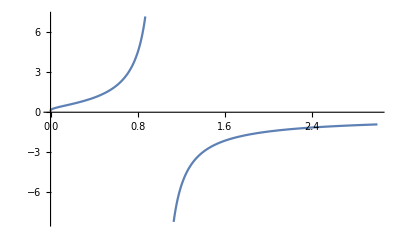

```mathematica
Plot[-1/Log[x],{x,0,3}]
```